# Complex Variables Toolkit - Final Project

## This package will contain many visualization tools that allows one to understand how complex functions behave

## Complex plane to image plane

### makeImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
makeImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

```mathematica
Dimensions@gridPts
```

{}

### makeCirclePoints will make expanding circles given smallest radius, largest radius, and a step size

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,stepSize_]:=Module[
{ang, lists, pts},
ang=Range[0 Pi,2 Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,stepSize]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

{RGBColor[0.35896396471577874, 0.0230035003899709, 0.9365304867125854],RGBColor[0.489754213820504, 0.7064503680258263, 0.040720901788792396],RGBColor[0.6336017408098567, 0.2061685015888346, 0.11126980718811108],RGBColor[0.8666744348458928, 0.6857951309870132, 0.02796402686371602],RGBColor[0.7106764003113895, 0.19952315254908437, 0.04936414545203904],RGBColor[0.46388990317260914, 0.3263713647764277, 0.7178238336846066],RGBColor[0.5485469719041092, 0.9848610470321073, 0.07117620217542475]}

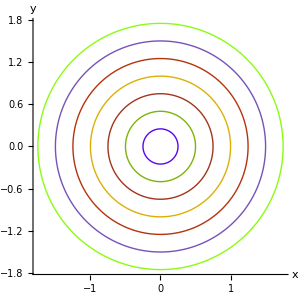
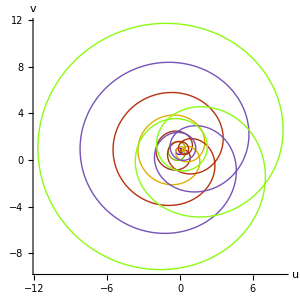

```mathematica
expr=(z+1)(z-.5)(z-1.5I);
pts=makeCirclePoints[.25,1.75,.25];
circleColors=makeRandomColors[pts]
n=2;
m=3;
makeImage[pts,expr,n,m,circleColors]
```

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
Clear[fSpace,makeVerticalPts,makeHorizontalPts,makeGridPts,makeLogVerticalPts,makeLogHorizontalPts,makeLogVerticalPts2,makeLogHorizontalPts2]
```

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]]]
```

```mathematica
makeVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[min,max,(max-min)/(ptsPerLine-1)]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[min,max,(max-min)/(ptsPerLine-1)]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[min,max,ptsPerLine,numLines];
horiPts=makeHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]

makeLogVerticalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[min,max,ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[Re[vertPts]]
]

makeLogHorizontalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[min,max,ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[Re[horiPts]]
]

makeLogGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]

makeLogVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posVertPts,negVertPts},
posVertPts=Table[Table[{x,y},{y,fSpace[.001,max,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[min,-.001,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]

makeLogHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posHoriPts,negHoriPts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,max,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[min,-.01,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
```

### old

```mathematica
makeVerticalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts},
newStep=stepSize+RandomReal[{.01,.02}];
vertPts=Table[Table[{x,y},{y,start,end,newStep}],{x,start,end,lineSpacing}];
Return[vertPts]
]

makeHorizontalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{horiPts},
newStep=stepSize+RandomReal[{.01,.02}];
horiPts=Table[Table[{x,y},{x,start,end,newStep}],{y,start,end,lineSpacing}];
Return[horiPts]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
```

### Equal space test constants

```mathematica
numPts=1000;
numLines=3;
min=-10;
max=10;
expr=z^3
```

z^3

#### first make vertical lines

{7,1,2}

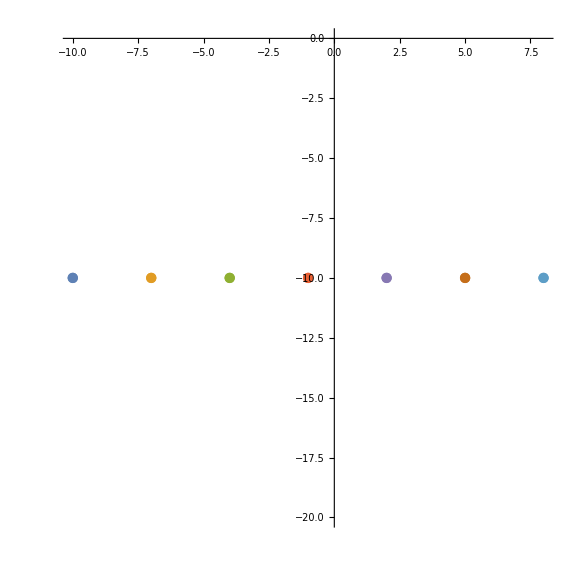

```mathematica
vertPts=makeVerticalPts[min,max,numPts,numLines];
Dimensions[vertPts]
ListPlot[vertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{7,1,2}

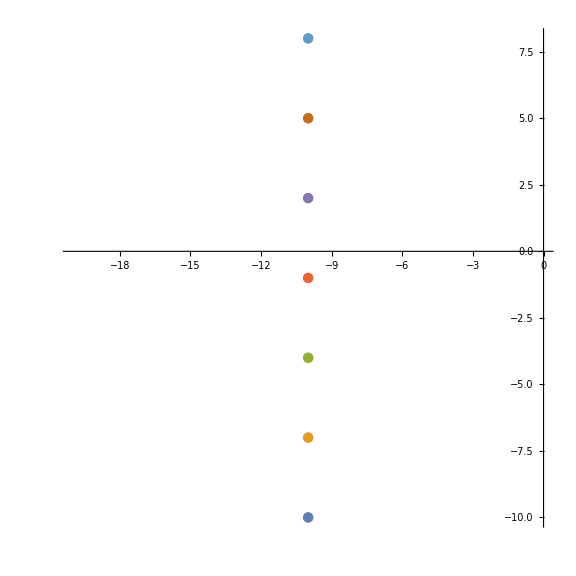

```mathematica
horiPts=makeHorizontalPts[min,max,numPts,numLines];
Dimensions[horiPts]
ListPlot[horiPts,ImageSize->Large,AspectRatio->1]
```

### Log test constants

```mathematica
ptsPerLine=100;
numLines=3;
min=-100;
max=100;
expr=z^3
```

z^3

{3,100,2}

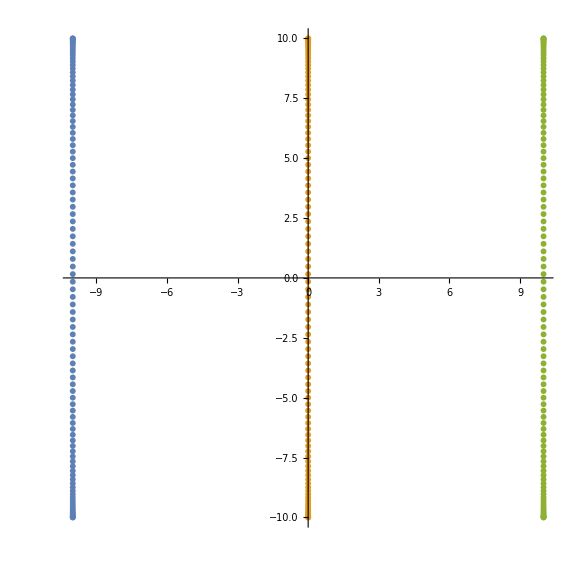

```mathematica
logVertPts=makeLogVerticalPts2[-10,10,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

```mathematica
Range[-10,10,20/(21-1)]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Log[0]
```

-∞

```mathematica
N@Re@Log[Range[-3,3,1/10]]
```

{1.09861,1.06471,1.02962,0.993252,0.955511,0.916291,0.875469,0.832909,0.788457,0.741937,0.693147,0.641854,0.587787,0.530628,0.470004,0.405465,0.336472,0.262364,0.182322,0.0953102,0.,-0.105361,-0.223144,-0.356675,-0.510826,-0.693147,-0.916291,-1.20397,-1.60944,-2.30259,-∞,-2.30259,-1.60944,-1.20397,-0.916291,-0.693147,-0.510826,-0.356675,-0.223144,-0.105361,0.,0.0953102,0.182322,0.262364,0.336472,0.405465,0.470004,0.530628,0.587787,0.641854,0.693147,0.741937,0.788457,0.832909,0.875469,0.916291,0.955511,0.993252,1.02962,1.06471,1.09861}

#### first make vertical lines

{3,100,2}

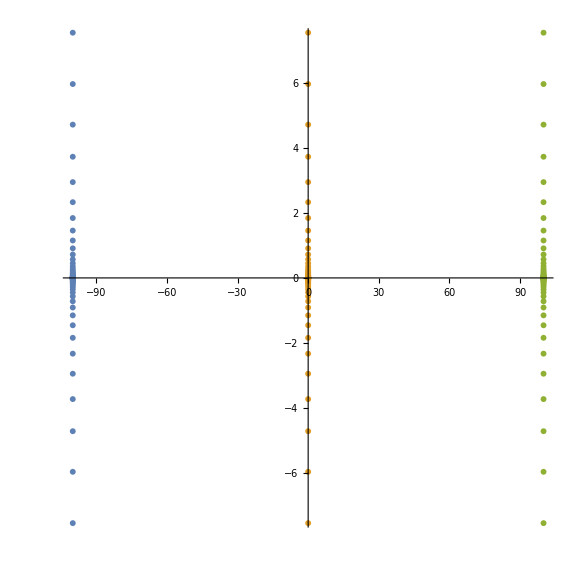

```mathematica
logVertPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{3,100,2}

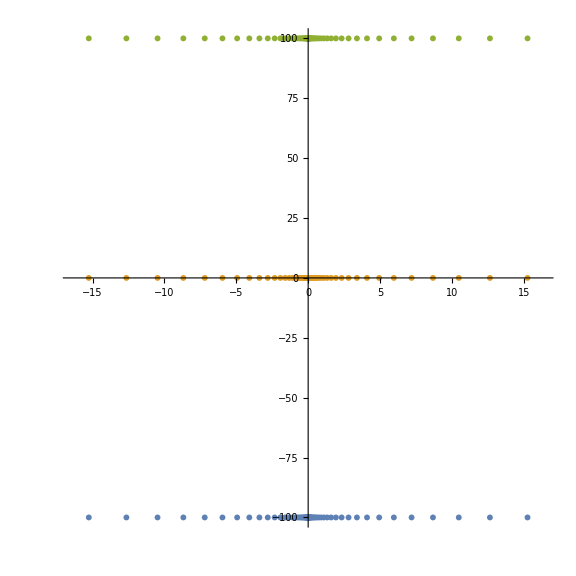

```mathematica
logHoriPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
Dimensions[logHoriPts]
ListPlot[logHoriPts,ImageSize->Large,AspectRatio->1]
```

### Next try to make a grid

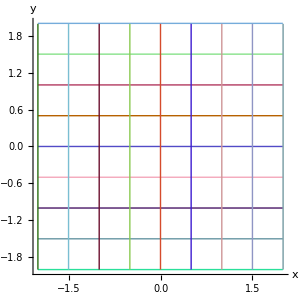
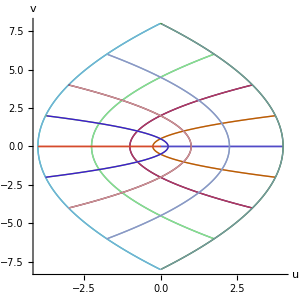

```mathematica
gridPts=makeGridPts[-2,2,.005,.5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

## Experiment with Riemann sphere stereographic projection

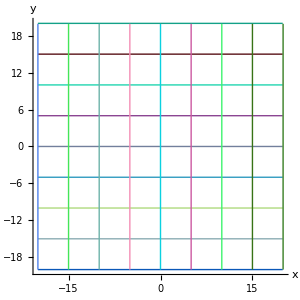
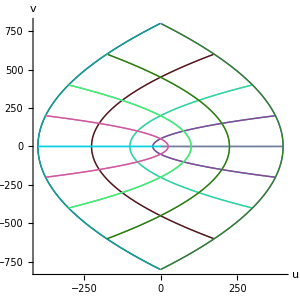

```mathematica
gridPts=makeGridPts[-20,20,.1,5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

```mathematica
gridPts[[1]][[1]]
```

{-20.,-20}

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

```mathematica
pts3D=complexTo3D[#]&/@#&/@gridPts;
colors3D=makeRandomColors[pts3D]
```

{RGBColor[0.24422795504472594, 0.718509724405566, 0.2942306690674845],RGBColor[0.5243284049279635, 0.920380228462925, 0.6964605504975374],RGBColor[0.3500580632475767, 0.1143063312157524, 0.9419621203035347],RGBColor[0.22927183484613156, 0.3507685255892832, 0.2645165512894019],RGBColor[0.019884690729763843, 0.10588292525076137, 0.3462999195282064],RGBColor[0.7737713297103055, 0.9952086351827802, 0.37285038029217366],RGBColor[0.26253185413077196, 0.21091154752364627, 0.8991616400015787],RGBColor[0.07484321994682341, 0.6523458430839548, 0.6472680582813906],RGBColor[0.8790292631647478, 0.22727488569853227, 0.7507164339642451],RGBColor[0.841715069758024, 0.9711700859886592, 0.982117167780503],RGBColor[0.9810623864819445, 0.8990194505692586, 0.14913857735350788],RGBColor[0.2432339800692329, 0.2891186741350298, 0.3522272948890761],RGBColor[0.025943534944733004, 0.2949711117710234, 0.980827164691142],RGBColor[0.20934497369691818, 0.08438416844971641, 0.5387624064714467],RGBColor[0.2232278749400649, 0.26545249064522025, 0.3381406227795072],RGBColor[0.3604798486951424, 0.6392870614954769, 0.335525518175976],RGBColor[0.08071137845420817, 0.11253602032061116, 0.2990364001119348],RGBColor[0.3879803490242031, 0.8171816551190056, 0.2936718484216516]}

```mathematica
ListPointPlot3D[pts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

### 1 to 100 log spaced

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]]]
```

```mathematica
Re@fSpace[-20,20,100]
```

{-20.,-19.9899,-19.9597,-19.9094,-19.8391,-19.7488,-19.6386,-19.5086,-19.359,-19.1899,-19.0014,-18.7939,-18.5674,-18.3222,-18.0585,-17.7767,-17.477,-17.1597,-16.8251,-16.4735,-16.1054,-15.7211,-15.3209,-14.9053,-14.4747,-14.0295,-13.5702,-13.0972,-12.6111,-12.1122,-11.6011,-11.0784,-10.5445,-10.,-9.44542,-8.88133,-8.3083,-7.7269,-7.13772,-6.54136,-5.93841,-5.32948,-4.71518,-4.09613,-3.47296,-2.8463,-2.21676,-1.585,-0.951638,-0.317319,0.317319,0.951638,1.585,2.21676,2.8463,3.47296,4.09613,4.71518,5.32948,5.93841,6.54136,7.13772,7.7269,8.3083,8.88133,9.44542,10.,10.5445,11.0784,11.6011,12.1122,12.6111,13.0972,13.5702,14.0295,14.4747,14.9053,15.3209,15.7211,16.1054,16.4735,16.8251,17.1597,17.477,17.7767,18.0585,18.3222,18.5674,18.7939,19.0014,19.1899,19.359,19.5086,19.6386,19.7488,19.8391,19.9094,19.9597,19.9899,20.}

```mathematica
Range[-1,1,(1-(-1))/(20-1)]
```

{-1,-17/19,-15/19,-13/19,-11/19,-9/19,-7/19,-5/19,-3/19,-1/19,1/19,3/19,5/19,7/19,9/19,11/19,13/19,15/19,17/19,1}

## Log grid Riemann sphere

```mathematica
ptsPerLine=100;
numLines=5;
min=-10000;
max=10000;
expr=z^3
```

z^3

```mathematica
logGridPts=makeLogGridPts[min,max,ptsPerLine,numLines];
Dimensions[logGridPts]
```

{10,100,2}

```mathematica
logPts3D=pts3D=complexTo3D[#]&/@#&/@logGridPts;
Dimensions[logPts3D]
```

{10,100,3}

```mathematica
colors3D=makeRandomColors[logPts3D]
```

{RGBColor[0.38523577310596013, 0.4893142078242385, 0.6506097010390894],RGBColor[0.28841745903896143, 0.9887386908047202, 0.403031232275854],RGBColor[0.6167726972277667, 0.34821094094007354, 0.026910213068668698],RGBColor[0.21062209648450136, 0.8639541313476129, 0.648159590145915],RGBColor[0.45171133252705253, 0.5270974162098963, 0.14666194301898638],RGBColor[0.4324944466793956, 0.7013055286397754, 0.5778877987891906],RGBColor[0.24725488685683872, 0.8894531336254243, 0.40283415363854425],RGBColor[0.47868103944640517, 0.17050336721965587, 0.9740693082239098],RGBColor[0.7522281302951963, 0.19536598643120606, 0.3898866132275203],RGBColor[0.5729816071124554, 0.8309972473725789, 0.34000036174733306]}

```mathematica
ListPointPlot3D[logPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

## Trying to get circular spaced points

```mathematica
Clear[makeRiemannUnitCirclePts]
```

```mathematica
makeRiemannUnitCirclePts[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
```

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannUnitCirclePts[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
```

```mathematica
sphericalPts=makeSphereSpacedPoints[20]
ListPlot[sphericalPts,PlotStyle->PointSize[.01],PlotRange->All]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

```mathematica
makeSphereSpacedPoints[20]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

```mathematica
horiPts=Table[Table[{x,y},{x,{1.,1.4005871438998048,2.045532694709038,3.3589407898715407,8.022471262465187,-24.177770864938736,-4.769218689284606,-2.5627803610641804,-1.67821653689189,-1.1806977689241733,-0.8469567964977006,-0.5958706627048448,-0.3902012108383555,-0.20967795044642917,-0.04136030594326412,0.12464987000685275,0.2977128989636771,0.4888702109658738,0.7139862766522278,0.9999999999999998}}],{y,-1,1,(1-(-1))/(2-1)}]
```

{{{1.,-1},{1.40059,-1},{2.04553,-1},{3.35894,-1},{8.02247,-1},{-24.1778,-1},{-4.76922,-1},{-2.56278,-1},{-1.67822,-1},{-1.1807,-1},{-0.846957,-1},{-0.595871,-1},{-0.390201,-1},{-0.209678,-1},{-0.0413603,-1},{0.12465,-1},{0.297713,-1},{0.48887,-1},{0.713986,-1},{1.,-1}},{{1.,1},{1.40059,1},{2.04553,1},{3.35894,1},{8.02247,1},{-24.1778,1},{-4.76922,1},{-2.56278,1},{-1.67822,1},{-1.1807,1},{-0.846957,1},{-0.595871,1},{-0.390201,1},{-0.209678,1},{-0.0413603,1},{0.12465,1},{0.297713,1},{0.48887,1},{0.713986,1},{1.,1}}}

```mathematica
makeHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,makeSphereSpacedPoints[ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,makeSphereSpacedPoints[ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
horiPts=makeVerticalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
```

```mathematica
makeHorizontalLines[-3,3,2000,4]
```

Part::partd: Part specification {x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,«1950»}⟦All,1⟧ is longer than depth of object.

Table::iterb: Iterator {x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,«1950»}⟦All,1⟧} does not have appropriate bounds.

Part::partd: Part specification {x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,«1950»}⟦All,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Table::iterb: Iterator {x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,«1950»}⟦All,1⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{Table[{x,y},{x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}⟦All,1⟧}],Table[{x,y},{x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}⟦All,1⟧}],Table[{x,y},{x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}⟦All,1⟧}],Table[{x,y},{x,{x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x,x}⟦All,1⟧}]}